Constants
h=6.626*10^-34;(* J s*)
k=1.38*10^-23;(* J K^-1*)
c=2.998*10^8;(* m s^-1*)
A=10^-10;

h=6.626*10^-27; (*erg s*)
k=1.38*10^-16; (*erg K^-1*)
c=2.998*10^10; (*cm s^-1*)
A=10^-8;

```mathematica
Remove["Global`*"]
B[λ_]:=(2 h c^2)/λ^5 1/(Exp[(h c)/(λ k T)]-1);
h=6.626*10^-27; (*erg s*)
k=1.38*10^-16; (*erg K^-1*)
c=2.998*10^10; (*cm s^-1*)
A=10^-8;
λion=912 A ;(*Angstrom*)
Tion=(h c)/(λion k);
T={10000,20000,40000};
EREC=Table[(h c)/(λion k T[[i]])NIntegrate[x^2/(Exp[x]-1),{x,∞,Tion/T[[i]]}]/NIntegrate[x^3/(Exp[x]-1),{x,Tion/T[[i]],0}],{i,{1,2,3}}]
```

{0.0000960023,0.037974,0.513478}

```mathematica
B2[λ_,𝒯_]=(2 h c^2)/λ^5 1/(Exp[(h c)/(λ k 𝒯)]-1);
Lα=1215.67 A;
Hα=6562.86 A;
B2[Lα,T]
EWLα=Table[(((h c)/Lα (2/c^2((k T[[i]])/h)^3) )NIntegrate[-x^2/(Exp[x]-1),{x,∞,Tion/T[[i]]}])/B2[Lα ,T[[i]]],{i,{1,2,3}}]/A 
EWHα=Table[(((h c)/Hα (2/c^2((k T[[i]])/h)^3) )(.4)NIntegrate[-x^2/(Exp[x]-1),{x,∞,Tion/T[[i]]}])/B2[Hα ,T[[i]]],{i,{1,2,3}}]/A (*Angstroms*)
```

{3.23139×10^14,1.20724×10^17,2.45103×10^18}

{4.0148,65.1537,425.477}

{0.0782637,118.798,5768.7}

Problem 3

```mathematica
Remove["Global`*"]
h=6.626*10^-27; (*erg s*)
k=1.38*10^-16; (*erg K^-1*)
c=2.998*10^10; (*cm s^-1*)
A=10^-8;
Hα=6562.86 A;
DL=3300; (*Mpc*)
Mdot=30; (*Msun/yr*)
FHα=(1.06 10^-9)(Mdot)(1/DL)^2  *10^(-1/2.5)

SHα=FHα(.2 (π *(650/2)^2));
NHα=SHα/(h c/Hα)
m=17;
F0=3.631*10^-20;
Fsky=F0 10^(m/-2.5);
R=1000;
νHα=c/Hα;
Δν=νHα/R;
Ssky=Fsky (.2)(π ((650/2)^2))Δν
Nsky=Ssky/(h c/ Hα)
τ=3*60*60
NHα/(√(NHα+Nsky))√τ
```

1.16252×10^-15

25.4892

1.74466×10^-10

57.6397

10800

290.531

## Problem 4 --- Closed box model

Ms[<Z]

(-1+(1-(z ν)/p)^(-1+1/ν))/(-1+ν)

Metallicity Distribution

(p (1-(z ν)/p)^(1/ν))/(p-z ν)^2

0.5

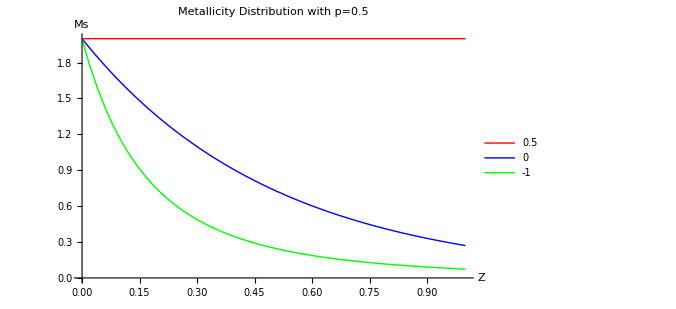

{0.1,0.0951626,0.0867769}

```mathematica
Remove["Global`*"]
Mg0=1;
Z[t_]=Z[t]/.DSolve[{D[Z[t],t]==((p-Z[t] ν) D[Mg[t],t])/((ν-1)Mg[t]),Z[0]==0},Z[t],t][[1]]//Expand//Simplify;
Z[t]/.Mg[t]->Mg/.Mg[0]->1;
Integrate[%,{Mg,0,1},Assumptions->{ν<1}];
Mg[z_]=Mg0*(1-(z ν)/p)^((1-ν)/ν);
Print["Ms[<Z]"]
Ms[z_]=(Mg[z]-Mg0)/(ν-1)//Simplify
Print["Metallicity Distribution"]
ZDist[z_]=D[Ms[z],z]//Simplify
νo={0.5,0,-1};
Zd=Table[Limit[ZDist[z],ν->νo[[i]]],{i,{1,2,3}}]//Simplify;
p=.5
Plot[Zd,{z,0,1},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}},AxesLabel->{Style["Z",15],Style["Ms",15]},PlotLegends->νo,PlotLabel->Style["Metallicity Distribution with p=0.5",20],ImageSize->500]
Table[Limit[Ms[.1p],ν->νo[[i]]],{i,{1,2,3}}]//Simplify
```